```mathematica
H0=Simplify[D[Piecewise[{{0,x<-1},{0,x>1},{(1-2 x) (-1-x)^2,x<0},{(-1+x)^2 (1+2 x),x≥0}},x],x]]
```

Piecewise[{{6 (-1+x) x, 0<x<1}, {-6 x (1+x), -1<x<0}, {0, True}}]

```mathematica
H1=H0/.x->x-1
```

Piecewise[{{6 (-2+x) (-1+x), 0<-1+x<1}, {-6 (-1+x) x, -1<-1+x<0}, {0, True}}]

```mathematica
H2=H0/.x->x-2
```

Piecewise[{{6 (-3+x) (-2+x), 0<-2+x<1}, {-6 (-2+x) (-1+x), -1<-2+x<0}, {0, True}}]

```mathematica
S0=Simplify[D[Piecewise[{{0,x<-1},{0,x>1},{x (-1-x)^2,x<0},{(-1+x)^2 x,x≥0}},x],x]]
```

Piecewise[{{1-4 x+3 x^2, 0≤x<1}, {1+4 x+3 x^2, -1<x<0}, {0, True}}]

```mathematica
S1=S0/.x->x-1
```

Piecewise[{{1-4 (-1+x)+3 (-1+x)^2, 0≤-1+x<1}, {1+4 (-1+x)+3 (-1+x)^2, -1<-1+x<0}, {0, True}}]

```mathematica
S2=S0/.x->x-2
```

Piecewise[{{1-4 (-2+x)+3 (-2+x)^2, 0≤-2+x<1}, {1+4 (-2+x)+3 (-2+x)^2, -1<-2+x<0}, {0, True}}]

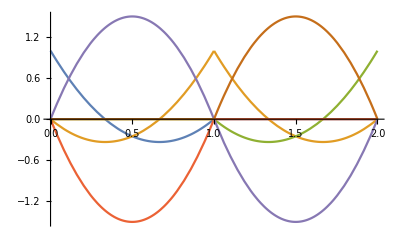

```mathematica
Plot[{S0,S1,S2,H0,H1,H2},{x,0,2}]
```

```mathematica
30Integrate[{{S1},{H1}}.{{S0,H0,S1,H1,S2,H2}},{x,0,2}]//MatrixForm
```

(-1 | 3 | 8 | 0 | -1 | -3
-3 | -36 | 0 | 72 | 3 | -36)

```mathematica
S3=S0/.x->x-3
```

Piecewise[{{1-4 (-3+x)+3 (-3+x)^2, 0≤-3+x<1}, {1+4 (-3+x)+3 (-3+x)^2, -1<-3+x<0}, {0, True}}]

```mathematica
S4=S0/.x->x-4
```

Piecewise[{{1-4 (-4+x)+3 (-4+x)^2, 0≤-4+x<1}, {1+4 (-4+x)+3 (-4+x)^2, -1<-4+x<0}, {0, True}}]

```mathematica
H3=H0/.x->x-3
```

Piecewise[{{6 (-4+x) (-3+x), 0<-3+x<1}, {-6 (-3+x) (-2+x), -1<-3+x<0}, {0, True}}]

```mathematica
H4=H0/.x->x-4
```

Piecewise[{{6 (-5+x) (-4+x), 0<-4+x<1}, {-6 (-4+x) (-3+x), -1<-4+x<0}, {0, True}}]

```mathematica
30Integrate[Transpose[{{H0,S1,H1,S2,H2,S3,H3,S4}}].{{H0,S1,H1,S2,H2,S3,H3,S4}},{x,1,2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 3 | -1 | -3 | 0 | 0 | 0
0 | 3 | 36 | 3 | -36 | 0 | 0 | 0
0 | -1 | 3 | 4 | -3 | 0 | 0 | 0
0 | -3 | -36 | -3 | 36 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
30Integrate[Transpose[{{S0,H0,S1,H1}}].{{S0,H0,S1,H1}},{x,0,1}]//MatrixForm
```

(4 | 3 | -1 | -3
3 | 36 | 3 | -36
-1 | 3 | 4 | -3
-3 | -36 | -3 | 36)

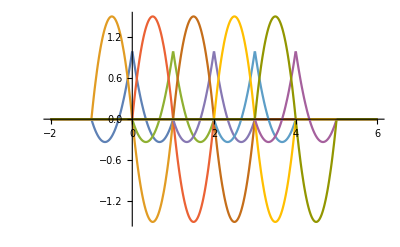

```mathematica
Plot[{S0,H0,S1,H1,S2,H2,S3,H3,S4,H4},{x,-2,6}]
```

```mathematica
<<ToMatlab`
```

```mathematica
S0
```

Piecewise[{{1-4 x+3 x^2, 0≤x<1}, {1+4 x+3 x^2, -1<x<0}, {0, True}}]

```mathematica
Simplify[S1]
```

Piecewise[{{8-10 x+3 x^2, 1≤x<2}, {x (-2+3 x), 0<x<1}, {0, True}}]

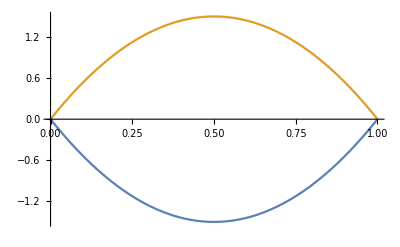

```mathematica
Plot[{H0,H1},{x,0,1}]
```

```mathematica
Simplify[TrigFactor[(Sin[x+Δ]-Sin[x])/Δ]]
```

(2 Cos[x+Δ/2] Sin[Δ/2])/Δ